Introduction to Calculus Tools.

Derivatives:-

```mathematica
D[Log[x], x]
```

1/x

```mathematica
D[x Log[x], x]
```

1+Log[x]

```mathematica
D[Log[x], {x,3}]
```

2/x^3

```mathematica
D[Log[x], {x,n}]
```

Piecewise[{{(-1)^(-1+n) x^-n (-1+n)!, n≥1}, {Log[x], True}}]

```mathematica
k = D[Log[x]/x,x]
```

1/x^2-Log[x]/x^2

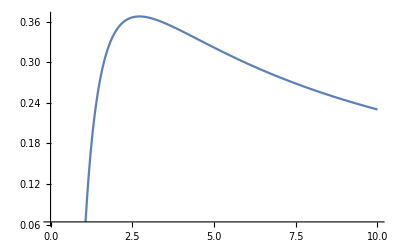

```mathematica
Plot[Log[x]/x, {x,0,10}]
```

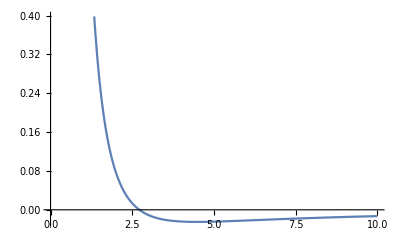

```mathematica
Plot[k, {x,0,10}]
```

```mathematica
x/.Solve[k==0, x]//N
```

{2.71828}

```mathematica
sol=Solve[2 x^2 + 2x - 1==0, x]
```

{{x→1/2 (-1-√3)},{x→1/2 (-1+√3)}}

```mathematica
sol[[2]]
```

{x→1/2 (-1+√3)}

```mathematica
sol[[1]]
```

{x→1/2 (-1-√3)}

```mathematica
x/.sol[[1]]
```

1/2 (-1-√3)

```mathematica
x/.sol[[2]]
```

1/2 (-1+√3)

```mathematica
2 x^2+2x-1/.sol[[2]]//Simplify
```

0

```mathematica
Integrate[Log[x]/x,{x,1,2}]//N
```

0.240227

```mathematica
Integrate[Log[x y]/x, x,y]
```

1/2 y (-2 Log[x]+Log[x y]^2)

```mathematica
Integrate[1/Sqrt[1+t+t^2], {t,0,1}]//Simplify//N
```

0.767652

```mathematica
NIntegrate[1/Sqrt[1+t+t^2], {t,0,1}]
```

0.767652

```mathematica
f[a_]= NIntegrate[1/Sqrt[1+a*t+t^2], {t,0,1}]
```

```mathematica
f[1]
```

0.767652

```mathematica
f[2]
```

0.693147

```mathematica
f[3]
```

0.638917

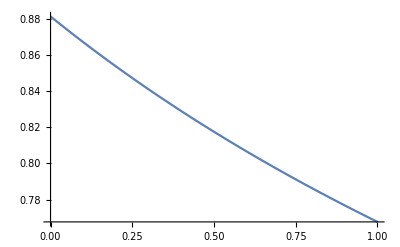

```mathematica
Plot[f[a], {a,0,1}]
```

Solving the differential equations...!

```mathematica
DSolve[x'[t] == -2x[t] , x[t] , t]
```

{{x[t]→ⅇ^(-2 t) C[1]}}

```mathematica
DSolve[{x'[t] == -2x[t] , x[0]==1},x[t] , t]
```

{{x[t]→ⅇ^(-2 t)}}

```mathematica
dsol=DSolve[{x'[t]==-y[t], y'[t] == -x[t], x[0]==2, y[0]==1}, {x[t], y[t]}, t]
```

{{x[t]→1/2 ⅇ^-t (3+ⅇ^(2 t)),y[t]→-1/2 ⅇ^-t (-3+ⅇ^(2 t))}}

```mathematica
X[t_]=x[t]/.dsol[[1]]
```

1/2 ⅇ^-t (3+ⅇ^(2 t))

```mathematica
Y[t_]=y[t]/.dsol[[1]]
```

-1/2 ⅇ^-t (-3+ⅇ^(2 t))

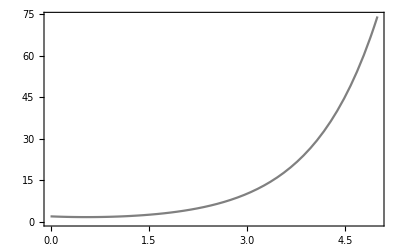

```mathematica
Plot[X[t], {t,0,5}, PlotStyle->Gray, Frame->True]
```

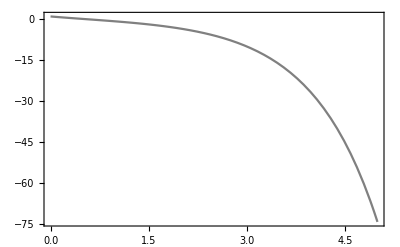

```mathematica
Plot[Y[t], {t,0,5}, Frame->True, PlotStyle->Gray]
```

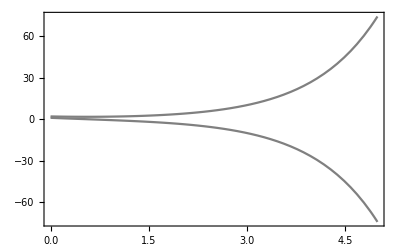

```mathematica
Plot[{X[t], Y[t]}, {t,0,5}, PlotStyle->Gray, Frame->True]
```

```mathematica
DSolve[z''[t]==-z[t] + z[t]^2, z[t], t]
```

Solve[(4 EllipticF[ArcSin[√((Root[3 C[1]-3 #1^2+2 #1^3&,3]-z[t])/(-Root[3 C[1]-3 #1^2+2 #1^3&,2]+Root[3 C[1]-3 #1^2+2 #1^3&,3]))],(Root[3 C[1]-3 #1^2+2 #1^3&,2]-Root[3 C[1]-3 #1^2+2 #1^3&,3])/(Root[3 C[1]-3 #1^2+2 #1^3&,1]-Root[3 C[1]-3 #1^2+2 #1^3&,3])]^2 (Root[3 C[1]-3 #1^2+2 #1^3&,2]-Root[3 C[1]-3 #1^2+2 #1^3&,3]) (-Root[3 C[1]-3 #1^2+2 #1^3&,1]+z[t]) (-Root[3 C[1]-3 #1^2+2 #1^3&,2]+z[t]) (-Root[3 C[1]-3 #1^2+2 #1^3&,3]+z[t]))/((-Root[3 C[1]-3 #1^2+2 #1^3&,1]+Root[3 C[1]-3 #1^2+2 #1^3&,3]) (-Root[3 C[1]-3 #1^2+2 #1^3&,2]+Root[3 C[1]-3 #1^2+2 #1^3&,3]) (C[1]-z[t]^2+(2 z[t]^3)/3))==(t+C[2])^2,z[t]]

```mathematica
dsol2= NDSolve[{z''[t]==-4z[t] - 0.5z'[t] z[t]^2, z[0]==1, z'[0]==0}, z[t], {t, 0,10}]
```

{{z[t]→InterpolatingFunction[…][t]}}

```mathematica
Z[t_]=z[t]/.dsol2[[1]]
```

InterpolatingFunction[…][t]

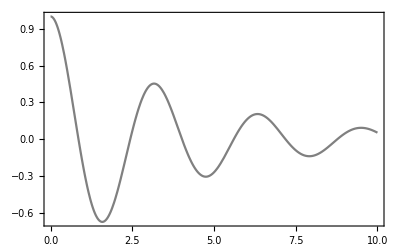

```mathematica
Plot[Z[t], {t,0,10}, Frame->True, PlotStyle->Gray]
```

Damped Oscillator